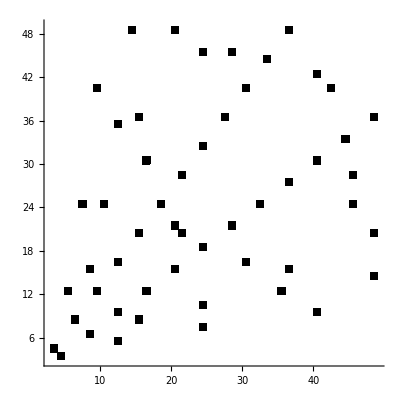

```mathematica
Graphics[
Table[
If[
Mod[Sqrt[a^2+b^2],1]==0,
Rectangle[{a,b}]
],
{a,1,50,1},
{b,1,50,1}
],
Axes-> True,
AxesOrigin->{0,0}
]
```

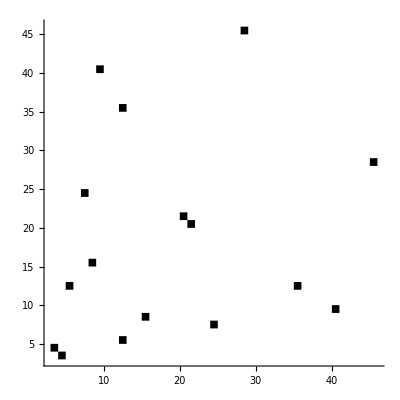

```mathematica
Graphics[
Table[
If[
GCD[a,b,Sqrt[a^2+b^2]]== 1 && IntegerQ[Sqrt[a^2+b^2]],
Rectangle[{a,b}]
],
{a,1,50,1},
{b,1,50,1}
],
Axes-> True,
AxesOrigin->{0,0}
]
```

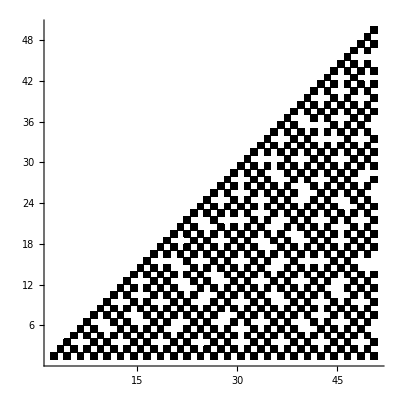

```mathematica
Graphics[
Table[
If[
GCD[m^2-n^2,2m n,m^2+n^2]==1,
Rectangle[{m,n}]
],
{m,2,50,1},
{n,1,m-1,1}
],
Axes-> True,
AxesOrigin->{0,0}
]
```

```mathematica
Manipulate[
Row[
{

m^2-n^2," ",2m n, " ",m^2+n^2," ",GCD[m^2-n^2,2m n, m^2+n^2],

Graphics[
{
Line[{{0,0},{2m n,0},{2m n,m^2-n^2},{0,0}}],
If[
GCD[m^2-n^2,2m n, m^2+n^2]>1,
{Gray,Triangle[{
{0,0},
{2m n/GCD[m^2-n^2,2m n, m^2+n^2],0},
{2m n/GCD[m^2-n^2,2m n, m^2+n^2],(m^2-n^2)/GCD[m^2-n^2,2m n, m^2+n^2]}
}]}
]
},
ImageSize->200
]

}
],
{{m,15},2,20,1,Appearance->"Labeled"},
{{n,6},1,15,1,Appearance->"Labeled"}
]
```